### Imports

```mathematica
(* kill everything *)
ClearAll["Global`*"]
Remove["Global`*"]
```

```mathematica
SetDirectory["C:\\Users\\Tal Miller\\Dropbox\\UNI\\Courses Graduate\\QFT\\Papers and Reviews\\Supersymmetric index and Localization\\Thesis\\Notebooks\\Star_shaped_quivers"];
```

```mathematica
<<"CharactersFunctions.m"
```

LieART 1.1.5

last revised 7 August 2014

Needs::nocont: Context LieART`BranchingRules` was not created when Needs was evaluated.

```mathematica
Get["C:\\Program Files\\Wolfram Research\\Mathematica\\11.0\\AddOns\\Applications\\LieART\\LieART.m"]
```

LieART 1.1.5

last revised 7 August 2014

Needs::nocont: Context LieART`BranchingRules` was not created when Needs was evaluated.

```mathematica
maxVarNum=6;
a=Table[Subscript["a",i],{i,maxVarNum}];
b=Table[Subscript["b",i],{i,maxVarNum}];
$Assumptions={r>0,r<1};
```

### SU(4) chars

#### Rep {1,0,0} (fundamental)

```mathematica
algebraClass=A;
repDynkinLabels={1,0,0};
rank=Length[repDynkinLabels];
dynkinToIrrep[repDynkinLabels,algebraClass]
char=   dynkinToChar[a,repDynkinLabels,algebraClass]
```

4

a_1+a_2+a_3+1/(a_2 a_3 a_1)

```mathematica
expr=haarMeasure[a,algebraClass,rank,type->"Short"] *charToHilbertIntegrand[a,r,char,rank]
```

((1-a_1/a_2) (1-a_1/a_3) (1-a_2/a_3) (1-a_1^2 a_2 a_3) (1-a_1 a_2^2 a_3) (1-a_1 a_2 a_3^2))/(a_1 a_2 a_3 (1-a_1 r) (1-a_2 r) (1-r/(a_1 a_2 a_3)) (1-a_3 r))

```mathematica
{calcTime,hilbertComponents}=calcHilbertIntegral[a,r,expr,1,rank,0,"Branches"]//Timing;
Print["calculation time = ", calcTime, " seconds = ", calcTime/60^2, " hours"];
```

Level = 1

Number of relevant poles = 2

Calculating residue for pole 1/2 in level 1

Calculating residue for pole 2/2 in level 1

Residue for pole 1/2 in level 1 is zero.

Residue for pole 2/2 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 1

Calculating residue for pole 1/1 in level 2

Residue for pole 1/1 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 1

Calculating residue for pole 1/1 in level 3

calculation time = 0.125 seconds = 0.0000347222 hours

```mathematica
hilbertFull=hilbertComponents//Flatten//Total//FullSimplify
```

1

Numeric divergence degree is 0.

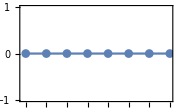

```mathematica
calcNumericDivergence[hilbertComponents]
```

#### Rep {1,0,0} + Rep {1,0,0}

```mathematica
algebraClass=A;
repDynkinLabels={1,0,0};
rank=Length[repDynkinLabels];
dynkinToIrrep[repDynkinLabels,algebraClass]
char1= dynkinToChar[a,repDynkinLabels,algebraClass]
```

4

a_1+a_2+a_3+1/(a_2 a_3 a_1)

```mathematica
algebraClass=A;
repDynkinLabels={1,0,0};
rank=Length[repDynkinLabels];
dynkinToIrrep[repDynkinLabels,algebraClass]
char2= dynkinToChar[a,repDynkinLabels,algebraClass]
```

4

a_1+a_2+a_3+1/(a_2 a_3 a_1)

```mathematica
expr=haarMeasure[a,algebraClass,rank,type->"Short"] *charToHilbertIntegrand[a,r,char1+char2,rank]
```

((1-a_1/a_2) (1-a_1/a_3) (1-a_2/a_3) (1-a_1^2 a_2 a_3) (1-a_1 a_2^2 a_3) (1-a_1 a_2 a_3^2))/(a_1 a_2 a_3 (1-a_1 r)^2 (1-a_2 r)^2 (1-r/(a_1 a_2 a_3))^2 (1-a_3 r)^2)

```mathematica
{calcTime,hilbertComponents}=calcHilbertIntegral[a,r,expr,1,rank,0,"Branches"]//Timing;
Print["calculation time = ", calcTime, " seconds = ", calcTime/60^2, " hours"];
```

Level = 1

Number of relevant poles = 2

Calculating residue for pole 1/2 in level 1

Calculating residue for pole 2/2 in level 1

Residue for pole 1/2 in level 1 is zero.

Residue for pole 2/2 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 2

Calculating residue for pole 1/2 in level 2

Calculating residue for pole 2/2 in level 2

Residue for pole 1/2 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 1

Calculating residue for pole 1/1 in level 3

Residue for pole 2/2 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 1

Calculating residue for pole 1/1 in level 3

calculation time = 0.21875 seconds = 0.0000607639 hours

```mathematica
hilbertFull=hilbertComponents//Flatten//Total//FullSimplify
```

1

```mathematica
calcNumericDivergence[hilbertComponents]
```

Numeric divergence degree is 0.

-Graphics-

#### Rep {1,0,0} + Rep {0,0,1}

```mathematica
algebraClass=A;
repDynkinLabels={1,0,0};
rank=Length[repDynkinLabels];
dynkinToIrrep[repDynkinLabels,algebraClass]
char1= dynkinToChar[a,repDynkinLabels,algebraClass]
```

4

a_1+a_2+a_3+1/(a_2 a_3 a_1)

```mathematica
algebraClass=A;
repDynkinLabels={0,0,1};
rank=Length[repDynkinLabels];
dynkinToIrrep[repDynkinLabels,algebraClass]
char2= dynkinToChar[a,repDynkinLabels,algebraClass]
```

OverBar[4]

a_1 a_2 a_3+1/a_1+1/a_2+1/a_3

```mathematica
expr=haarMeasure[a,algebraClass,rank,type->"Short"] *charToHilbertIntegrand[a,r,char1+char2,rank]
```

((1-a_1/a_2) (1-a_1/a_3) (1-a_2/a_3) (1-a_1^2 a_2 a_3) (1-a_1 a_2^2 a_3) (1-a_1 a_2 a_3^2))/(a_1 a_2 a_3 (1-r/a_1) (1-a_1 r) (1-r/a_2) (1-a_2 r) (1-r/a_3) (1-r/(a_1 a_2 a_3)) (1-a_3 r) (1-a_1 a_2 a_3 r))

```mathematica
{calcTime,hilbertComponents}=calcHilbertIntegral[a,r,expr,1,rank,0,"Branches"]//Timing;
Print["calculation time = ", calcTime, " seconds = ", calcTime/60^2, " hours"];
```

Level = 1

Number of relevant poles = 3

Calculating residue for pole 1/3 in level 1

Calculating residue for pole 2/3 in level 1

Calculating residue for pole 3/3 in level 1

Residue for pole 1/3 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 0

Residue for pole 2/3 in level 1 is zero.

Residue for pole 3/3 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 2

Calculating residue for pole 1/2 in level 2

Calculating residue for pole 2/2 in level 2

Residue for pole 1/2 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 1

Calculating residue for pole 1/1 in level 3

Residue for pole 2/2 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 2

Calculating residue for pole 1/2 in level 3

Calculating residue for pole 2/2 in level 3

calculation time = 0.453125 seconds = 0.000125868 hours

```mathematica
hilbertFull=hilbertComponents//Flatten//Total//FullSimplify
```

1/(1-r^2)

Numeric divergence degree is -0.998006

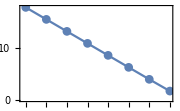

```mathematica
calcNumericDivergence[hilbertComponents]
```

#### Rep {0,1,0}

```mathematica
algebraClass=A;
repDynkinLabels={0,1,0};
rank=Length[repDynkinLabels];
dynkinToIrrep[repDynkinLabels,algebraClass]
char=   dynkinToChar[a,repDynkinLabels,algebraClass]
```

6

a_1 a_2+a_3 a_2+a_1 a_3+1/(a_1 a_3)+1/(a_1 a_2)+1/(a_3 a_2)

```mathematica
expr=haarMeasure[a,algebraClass,rank,type->"Short"] *charToHilbertIntegrand[a,r,char,rank]
```

((1-a_1/a_2) (1-a_1/a_3) (1-a_2/a_3) (1-a_1^2 a_2 a_3) (1-a_1 a_2^2 a_3) (1-a_1 a_2 a_3^2))/(a_1 a_2 a_3 (1-r/(a_1 a_2)) (1-a_1 a_2 r) (1-r/(a_1 a_3)) (1-r/(a_2 a_3)) (1-a_1 a_3 r) (1-a_2 a_3 r))

```mathematica
{calcTime,hilbertComponents}=calcHilbertIntegral[a,r,expr,1,rank,0,"Branches"]//Timing;
Print["calculation time = ", calcTime, " seconds = ", calcTime/60^2, " hours"];
```

Level = 1

Number of relevant poles = 3

Calculating residue for pole 1/3 in level 1

Calculating residue for pole 2/3 in level 1

Calculating residue for pole 3/3 in level 1

Residue for pole 1/3 in level 1 is zero.

Residue for pole 2/3 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 1

Calculating residue for pole 1/1 in level 2

Residue for pole 1/1 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 1

Calculating residue for pole 1/1 in level 3

Residue for pole 3/3 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 0

calculation time = 0.28125 seconds = 0.000078125 hours

```mathematica
hilbertFull=hilbertComponents//Flatten//Total//FullSimplify
```

1/(1-r^2)

```mathematica
calcNumericDivergence[hilbertComponents]
```

Numeric divergence degree is -0.998006

-Graphics-

#### Rep {0,1,0} + Rep {0,1,0}

```mathematica
algebraClass=A;
repDynkinLabels={0,1,0};
rank=Length[repDynkinLabels];
dynkinToIrrep[repDynkinLabels,algebraClass]
char=   dynkinToChar[a,repDynkinLabels,algebraClass]
```

6

a_1 a_2+a_3 a_2+a_1 a_3+1/(a_1 a_3)+1/(a_1 a_2)+1/(a_3 a_2)

```mathematica
expr=haarMeasure[a,algebraClass,rank,type->"Short"] *charToHilbertIntegrand[a,r,2*char,rank]
```

((1-a_1/a_2) (1-a_1/a_3) (1-a_2/a_3) (1-a_1^2 a_2 a_3) (1-a_1 a_2^2 a_3) (1-a_1 a_2 a_3^2))/(a_1 a_2 a_3 (1-r/(a_1 a_2))^2 (1-a_1 a_2 r)^2 (1-r/(a_1 a_3))^2 (1-r/(a_2 a_3))^2 (1-a_1 a_3 r)^2 (1-a_2 a_3 r)^2)

```mathematica
{calcTime,hilbertComponents}=calcHilbertIntegral[a,r,expr,1,rank,0,"Branches"]//Timing;
Print["calculation time = ", calcTime, " seconds = ", calcTime/60^2, " hours"];
```

Level = 1

Number of relevant poles = 3

Calculating residue for pole 1/3 in level 1

Calculating residue for pole 2/3 in level 1

Calculating residue for pole 3/3 in level 1

Residue for pole 1/3 in level 1 is zero.

Residue for pole 2/3 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 3

Calculating residue for pole 1/3 in level 2

Calculating residue for pole 2/3 in level 2

Calculating residue for pole 3/3 in level 2

Residue for pole 1/3 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 1

Calculating residue for pole 1/1 in level 3

Residue for pole 2/3 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 1

Calculating residue for pole 1/1 in level 3

Residue for pole 3/3 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 0

Residue for pole 3/3 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 1

Calculating residue for pole 1/1 in level 2

Residue for pole 1/1 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 1

Calculating residue for pole 1/1 in level 3

calculation time = 0.765625 seconds = 0.000212674 hours

```mathematica
hilbertFull=hilbertComponents//Flatten//Total//FullSimplify
```

-1/((r^2-1)^3)

Numeric divergence degree is -2.99402

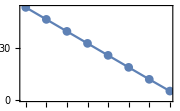

```mathematica
calcNumericDivergence[hilbertComponents]
```

#### Rep {2,0,0}

```mathematica
algebraClass=A;
repDynkinLabels={2,0,0};
rank=Length[repDynkinLabels];
dynkinToIrrep[repDynkinLabels,algebraClass]
char=   dynkinToChar[a,repDynkinLabels,algebraClass]
```

10

a_1^2+a_2 a_1+a_3 a_1+a_2^2+a_3^2+a_2 a_3+1/(a_2 a_3)+1/(a_2 a_1)+1/(a_3 a_1)+1/(a_2^2 a_3^2 a_1^2)

```mathematica
expr=haarMeasure[a,algebraClass,rank,type->"Short"] *charToHilbertIntegrand[a,r,char,rank]
```

((1-a_1/a_2) (1-a_1/a_3) (1-a_2/a_3) (1-a_1^2 a_2 a_3) (1-a_1 a_2^2 a_3) (1-a_1 a_2 a_3^2))/(a_1 a_2 a_3 (1-a_1^2 r) (1-r/(a_1 a_2)) (1-a_1 a_2 r) (1-a_2^2 r) (1-r/(a_1^2 a_2^2 a_3^2)) (1-r/(a_1 a_3)) (1-r/(a_2 a_3)) (1-a_1 a_3 r) (1-a_2 a_3 r) (1-a_3^2 r))

```mathematica
{calcTime,hilbertComponents}=calcHilbertIntegral[a,r,expr,1,rank,0,"Branches"]//Timing;
Print["calculation time = ", calcTime, " seconds = ", calcTime/60^2, " hours"];
```

Level = 1

Number of relevant poles = 5

Calculating residue for pole 1/5 in level 1

Calculating residue for pole 2/5 in level 1

Calculating residue for pole 3/5 in level 1

Calculating residue for pole 4/5 in level 1

Calculating residue for pole 5/5 in level 1

Residue for pole 1/5 in level 1 is zero.

Residue for pole 2/5 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 3

Calculating residue for pole 1/3 in level 2

Calculating residue for pole 2/3 in level 2

Calculating residue for pole 3/3 in level 2

Residue for pole 1/3 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 0

Residue for pole 2/3 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 0

Residue for pole 3/3 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 0

Residue for pole 3/5 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 4

Calculating residue for pole 1/4 in level 2

Calculating residue for pole 2/4 in level 2

Calculating residue for pole 3/4 in level 2

Calculating residue for pole 4/4 in level 2

Residue for pole 1/4 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 2

Calculating residue for pole 1/2 in level 3

Calculating residue for pole 2/2 in level 3

Residue for pole 2/4 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 1

Calculating residue for pole 1/1 in level 3

Residue for pole 3/4 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 3

Calculating residue for pole 1/3 in level 3

Calculating residue for pole 2/3 in level 3

Calculating residue for pole 3/3 in level 3

Residue for pole 4/4 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 3

Calculating residue for pole 1/3 in level 3

Calculating residue for pole 2/3 in level 3

Calculating residue for pole 3/3 in level 3

Residue for pole 4/5 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 4

Calculating residue for pole 1/4 in level 2

Calculating residue for pole 2/4 in level 2

Calculating residue for pole 3/4 in level 2

Calculating residue for pole 4/4 in level 2

Residue for pole 1/4 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 1

Calculating residue for pole 1/1 in level 3

Residue for pole 2/4 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 2

Calculating residue for pole 1/2 in level 3

Calculating residue for pole 2/2 in level 3

Residue for pole 3/4 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 3

Calculating residue for pole 1/3 in level 3

Calculating residue for pole 2/3 in level 3

Calculating residue for pole 3/3 in level 3

Residue for pole 4/4 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 3

Calculating residue for pole 1/3 in level 3

Calculating residue for pole 2/3 in level 3

Calculating residue for pole 3/3 in level 3

Residue for pole 5/5 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 0

calculation time = 1.625 seconds = 0.000451389 hours

```mathematica
hilbertFull=hilbertComponents//Flatten//Total//FullSimplify
```

1/(1-r^4)

Numeric divergence degree is -0.994119

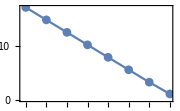

```mathematica
calcNumericDivergence[hilbertComponents]
```

#### Rep {2,0,0} + Rep {2,0,0}

```mathematica
algebraClass=A;
repDynkinLabels={2,0,0};
rank=Length[repDynkinLabels];
dynkinToIrrep[repDynkinLabels,algebraClass]
char1= dynkinToChar[a,repDynkinLabels,algebraClass]
```

10

a_1^2+a_2 a_1+a_3 a_1+a_2^2+a_3^2+a_2 a_3+1/(a_2 a_3)+1/(a_2 a_1)+1/(a_3 a_1)+1/(a_2^2 a_3^2 a_1^2)

```mathematica
algebraClass=A;
repDynkinLabels={2,0,0};
rank=Length[repDynkinLabels];
dynkinToIrrep[repDynkinLabels,algebraClass]
char2= dynkinToChar[a,repDynkinLabels,algebraClass]
```

10

a_1^2+a_2 a_1+a_3 a_1+a_2^2+a_3^2+a_2 a_3+1/(a_2 a_3)+1/(a_2 a_1)+1/(a_3 a_1)+1/(a_2^2 a_3^2 a_1^2)

```mathematica
expr=haarMeasure[a,algebraClass,rank,type->"Short"] *charToHilbertIntegrand[a,r,char1+char2,rank]
```

((1-a_1/a_2) (1-a_1/a_3) (1-a_2/a_3) (1-a_1^2 a_2 a_3) (1-a_1 a_2^2 a_3) (1-a_1 a_2 a_3^2))/(a_1 a_2 a_3 (1-a_1^2 r)^2 (1-r/(a_1 a_2))^2 (1-a_1 a_2 r)^2 (1-a_2^2 r)^2 (1-r/(a_1^2 a_2^2 a_3^2))^2 (1-r/(a_1 a_3))^2 (1-r/(a_2 a_3))^2 (1-a_1 a_3 r)^2 (1-a_2 a_3 r)^2 (1-a_3^2 r)^2)

```mathematica
{calcTime,hilbertComponents}=calcHilbertIntegral[a,r,expr,1,rank,0,"Branches"]//Timing;
Print["calculation time = ", calcTime, " seconds = ", calcTime/60^2, " hours"];
```

Level = 1

Number of relevant poles = 5

Calculating residue for pole 1/5 in level 1

Calculating residue for pole 2/5 in level 1

Calculating residue for pole 3/5 in level 1

Calculating residue for pole 4/5 in level 1

Calculating residue for pole 5/5 in level 1

Residue for pole 1/5 in level 1 is zero.

Residue for pole 2/5 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 4

Calculating residue for pole 1/4 in level 2

Calculating residue for pole 2/4 in level 2

Calculating residue for pole 3/4 in level 2

Calculating residue for pole 4/4 in level 2

Residue for pole 1/4 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 1

Calculating residue for pole 1/1 in level 3

Residue for pole 2/4 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 1

Calculating residue for pole 1/1 in level 3

Residue for pole 3/4 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 0

Residue for pole 4/4 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 2

Calculating residue for pole 1/2 in level 3

Calculating residue for pole 2/2 in level 3

Residue for pole 3/5 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 3

Calculating residue for pole 1/3 in level 2

Calculating residue for pole 2/3 in level 2

Calculating residue for pole 3/3 in level 2

Residue for pole 1/3 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 1

Calculating residue for pole 1/1 in level 3

Residue for pole 2/3 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 2

Calculating residue for pole 1/2 in level 3

Calculating residue for pole 2/2 in level 3

Residue for pole 3/3 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 2

Calculating residue for pole 1/2 in level 3

Calculating residue for pole 2/2 in level 3

Residue for pole 4/5 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 3

Calculating residue for pole 1/3 in level 2

Calculating residue for pole 2/3 in level 2

Calculating residue for pole 3/3 in level 2

Residue for pole 1/3 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 1

Calculating residue for pole 1/1 in level 3

Residue for pole 2/3 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 2

Calculating residue for pole 1/2 in level 3

Calculating residue for pole 2/2 in level 3

Residue for pole 3/3 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 2

Calculating residue for pole 1/2 in level 3

Calculating residue for pole 2/2 in level 3

Residue for pole 5/5 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 1

Calculating residue for pole 1/1 in level 2

Residue for pole 1/1 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 2

Calculating residue for pole 1/2 in level 3

Calculating residue for pole 2/2 in level 3

calculation time = 8.09375 seconds = 0.00224826 hours

```mathematica
hilbertFull=hilbertComponents//Flatten//Total//FullSimplify
```

-1/((r^4-1)^5)

Numeric divergence degree is -4.97059

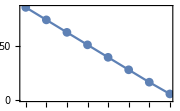

```mathematica
calcNumericDivergence[hilbertComponents]
```

#### Rep {2,0,0} + Rep {0,0,2}

```mathematica
algebraClass=A;
repDynkinLabels={2,0,0};
rank=Length[repDynkinLabels];
dynkinToIrrep[repDynkinLabels,algebraClass]
char1= dynkinToChar[a,repDynkinLabels,algebraClass]
```

10

a_1^2+a_2 a_1+a_3 a_1+a_2^2+a_3^2+a_2 a_3+1/(a_2 a_3)+1/(a_2 a_1)+1/(a_3 a_1)+1/(a_2^2 a_3^2 a_1^2)

```mathematica
algebraClass=A;
repDynkinLabels={0,0,2};
rank=Length[repDynkinLabels];
dynkinToIrrep[repDynkinLabels,algebraClass]
char2= dynkinToChar[a,repDynkinLabels,algebraClass]
```

OverBar[10]

a_1^2 a_2^2 a_3^2+a_1 a_3+a_2 a_3+a_1 a_2+1/(a_1 a_2)+1/a_1^2+1/a_2^2+1/(a_1 a_3)+1/(a_2 a_3)+1/a_3^2

```mathematica
expr=haarMeasure[a,algebraClass,rank,type->"Short"] *charToHilbertIntegrand[a,r,char1+char2,rank]
```

((1-a_1/a_2) (1-a_1/a_3) (1-a_2/a_3) (1-a_1^2 a_2 a_3) (1-a_1 a_2^2 a_3) (1-a_1 a_2 a_3^2))/(a_1 a_2 a_3 (1-r/a_1^2) (1-a_1^2 r) (1-r/a_2^2) (1-r/(a_1 a_2))^2 (1-a_1 a_2 r)^2 (1-a_2^2 r) (1-r/a_3^2) (1-r/(a_1^2 a_2^2 a_3^2)) (1-r/(a_1 a_3))^2 (1-r/(a_2 a_3))^2 (1-a_1 a_3 r)^2 (1-a_2 a_3 r)^2 (1-a_3^2 r) (1-a_1^2 a_2^2 a_3^2 r))

```mathematica
{calcTime,hilbertComponents}=calcHilbertIntegral[a,r,expr,1,rank,0,"Branches"]//Timing;
Print["calculation time = ", calcTime, " seconds = ", calcTime/60^2, " hours"];
```

Level = 1

Number of relevant poles = 7

Calculating residue for pole 1/7 in level 1

Calculating residue for pole 2/7 in level 1

Calculating residue for pole 3/7 in level 1

Calculating residue for pole 4/7 in level 1

Calculating residue for pole 5/7 in level 1

Calculating residue for pole 6/7 in level 1

Calculating residue for pole 7/7 in level 1

Residue for pole 1/7 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 3

Calculating residue for pole 1/3 in level 2

Calculating residue for pole 2/3 in level 2

Calculating residue for pole 3/3 in level 2

Residue for pole 1/3 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 2

Calculating residue for pole 1/2 in level 3

Calculating residue for pole 2/2 in level 3

Residue for pole 2/3 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 2

Calculating residue for pole 1/2 in level 3

Calculating residue for pole 2/2 in level 3

Residue for pole 3/3 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 5

Calculating residue for pole 1/5 in level 3

Calculating residue for pole 2/5 in level 3

Calculating residue for pole 3/5 in level 3

Calculating residue for pole 4/5 in level 3

Calculating residue for pole 5/5 in level 3

Residue for pole 2/7 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 3

Calculating residue for pole 1/3 in level 2

Calculating residue for pole 2/3 in level 2

Calculating residue for pole 3/3 in level 2

Residue for pole 1/3 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 2

Calculating residue for pole 1/2 in level 3

Calculating residue for pole 2/2 in level 3

Residue for pole 2/3 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 2

Calculating residue for pole 1/2 in level 3

Calculating residue for pole 2/2 in level 3

Residue for pole 3/3 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 5

Calculating residue for pole 1/5 in level 3

Calculating residue for pole 2/5 in level 3

Calculating residue for pole 3/5 in level 3

Calculating residue for pole 4/5 in level 3

Calculating residue for pole 5/5 in level 3

Residue for pole 3/7 in level 1 is zero.

Residue for pole 4/7 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 6

Calculating residue for pole 1/6 in level 2

Calculating residue for pole 2/6 in level 2

Calculating residue for pole 3/6 in level 2

Calculating residue for pole 4/6 in level 2

Calculating residue for pole 5/6 in level 2

Calculating residue for pole 6/6 in level 2

Residue for pole 1/6 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 2

Calculating residue for pole 1/2 in level 3

Calculating residue for pole 2/2 in level 3

Residue for pole 2/6 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 2

Calculating residue for pole 1/2 in level 3

Calculating residue for pole 2/2 in level 3

Residue for pole 3/6 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 3

Calculating residue for pole 1/3 in level 3

Calculating residue for pole 2/3 in level 3

Calculating residue for pole 3/3 in level 3

Residue for pole 4/6 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 3

Calculating residue for pole 1/3 in level 3

Calculating residue for pole 2/3 in level 3

Calculating residue for pole 3/3 in level 3

Residue for pole 5/6 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 2

Calculating residue for pole 1/2 in level 3

Calculating residue for pole 2/2 in level 3

Residue for pole 6/6 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 4

Calculating residue for pole 1/4 in level 3

Calculating residue for pole 2/4 in level 3

Calculating residue for pole 3/4 in level 3

Calculating residue for pole 4/4 in level 3

Residue for pole 5/7 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 5

Calculating residue for pole 1/5 in level 2

Calculating residue for pole 2/5 in level 2

Calculating residue for pole 3/5 in level 2

Calculating residue for pole 4/5 in level 2

Calculating residue for pole 5/5 in level 2

Residue for pole 1/5 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 3

Calculating residue for pole 1/3 in level 3

Calculating residue for pole 2/3 in level 3

Calculating residue for pole 3/3 in level 3

Residue for pole 2/5 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 3

Calculating residue for pole 1/3 in level 3

Calculating residue for pole 2/3 in level 3

Calculating residue for pole 3/3 in level 3

Residue for pole 3/5 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 3

Calculating residue for pole 1/3 in level 3

Calculating residue for pole 2/3 in level 3

Calculating residue for pole 3/3 in level 3

Residue for pole 4/5 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 4

Calculating residue for pole 1/4 in level 3

Calculating residue for pole 2/4 in level 3

Calculating residue for pole 3/4 in level 3

Calculating residue for pole 4/4 in level 3

Residue for pole 5/5 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 4

Calculating residue for pole 1/4 in level 3

Calculating residue for pole 2/4 in level 3

Calculating residue for pole 3/4 in level 3

Calculating residue for pole 4/4 in level 3

Residue for pole 6/7 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 5

Calculating residue for pole 1/5 in level 2

Calculating residue for pole 2/5 in level 2

Calculating residue for pole 3/5 in level 2

Calculating residue for pole 4/5 in level 2

Calculating residue for pole 5/5 in level 2

Residue for pole 1/5 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 3

Calculating residue for pole 1/3 in level 3

Calculating residue for pole 2/3 in level 3

Calculating residue for pole 3/3 in level 3

Residue for pole 2/5 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 3

Calculating residue for pole 1/3 in level 3

Calculating residue for pole 2/3 in level 3

Calculating residue for pole 3/3 in level 3

Residue for pole 3/5 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 3

Calculating residue for pole 1/3 in level 3

Calculating residue for pole 2/3 in level 3

Calculating residue for pole 3/3 in level 3

Residue for pole 4/5 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 4

Calculating residue for pole 1/4 in level 3

Calculating residue for pole 2/4 in level 3

Calculating residue for pole 3/4 in level 3

Calculating residue for pole 4/4 in level 3

Residue for pole 5/5 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 4

Calculating residue for pole 1/4 in level 3

Calculating residue for pole 2/4 in level 3

Calculating residue for pole 3/4 in level 3

Calculating residue for pole 4/4 in level 3

Residue for pole 7/7 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 3

Calculating residue for pole 1/3 in level 2

Calculating residue for pole 2/3 in level 2

Calculating residue for pole 3/3 in level 2

Residue for pole 1/3 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 5

Calculating residue for pole 1/5 in level 3

Calculating residue for pole 2/5 in level 3

Calculating residue for pole 3/5 in level 3

Calculating residue for pole 4/5 in level 3

Calculating residue for pole 5/5 in level 3

Residue for pole 2/3 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 5

Calculating residue for pole 1/5 in level 3

Calculating residue for pole 2/5 in level 3

Calculating residue for pole 3/5 in level 3

Calculating residue for pole 4/5 in level 3

Calculating residue for pole 5/5 in level 3

Residue for pole 3/3 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 6

Calculating residue for pole 1/6 in level 3

Calculating residue for pole 2/6 in level 3

Calculating residue for pole 3/6 in level 3

Calculating residue for pole 4/6 in level 3

Calculating residue for pole 5/6 in level 3

Calculating residue for pole 6/6 in level 3

calculation time = 15.125 seconds = 0.00420139 hours

```mathematica
hilbertFull=hilbertComponents//Flatten//Total//FullSimplify
```

-1/((r^2-1)^5 (r^2+1)^3 (r^4+r^2+1))

Numeric divergence degree is -4.97073

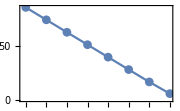

```mathematica
calcNumericDivergence[hilbertComponents]
```

#### Rep {1,0,1} (adjoint)

```mathematica
algebraClass=A;
repDynkinLabels={1,0,1};
rank=Length[repDynkinLabels];
dynkinToIrrep[repDynkinLabels,algebraClass]
char=   dynkinToChar[a,repDynkinLabels,algebraClass]
```

15

a_2 a_3 a_1^2+a_2 a_3^2 a_1+a_2^2 a_3 a_1+a_1/a_2+a_1/a_3+a_3/a_2+a_2/a_3+a_2/a_1+a_3/a_1+1/(a_2^2 a_3 a_1)+1/(a_2 a_3^2 a_1)+1/(a_2 a_3 a_1^2)+3

```mathematica
expr=haarMeasure[a,algebraClass,rank,type->"Short"] *charToHilbertIntegrand[a,r,char,rank]
```

((1-a_1/a_2) (1-a_1/a_3) (1-a_2/a_3) (1-a_1^2 a_2 a_3) (1-a_1 a_2^2 a_3) (1-a_1 a_2 a_3^2))/(a_1 a_2 a_3 (1-r)^3 (1-(a_1 r)/a_2) (1-(a_2 r)/a_1) (1-r/(a_1 a_2 a_3^2)) (1-(a_1 r)/a_3) (1-r/(a_1 a_2^2 a_3)) (1-r/(a_1^2 a_2 a_3)) (1-(a_2 r)/a_3) (1-(a_3 r)/a_1) (1-(a_3 r)/a_2) (1-a_1^2 a_2 a_3 r) (1-a_1 a_2^2 a_3 r) (1-a_1 a_2 a_3^2 r))

```mathematica
{calcTime,hilbertComponents}=calcHilbertIntegral[a,r,expr,1,rank,0,"Branches"]//Timing;
Print["calculation time = ", calcTime, " seconds = ", calcTime/60^2, " hours"];
```

Level = 1

Number of relevant poles = 7

Calculating residue for pole 1/7 in level 1

Calculating residue for pole 2/7 in level 1

Calculating residue for pole 3/7 in level 1

Calculating residue for pole 4/7 in level 1

Calculating residue for pole 5/7 in level 1

Calculating residue for pole 6/7 in level 1

Calculating residue for pole 7/7 in level 1

Residue for pole 1/7 in level 1 is zero.

Residue for pole 2/7 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 1

Calculating residue for pole 1/1 in level 2

Residue for pole 1/1 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 0

Residue for pole 3/7 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 4

Calculating residue for pole 1/4 in level 2

Calculating residue for pole 2/4 in level 2

Calculating residue for pole 3/4 in level 2

Calculating residue for pole 4/4 in level 2

Residue for pole 1/4 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 5

Calculating residue for pole 1/5 in level 3

Calculating residue for pole 2/5 in level 3

Calculating residue for pole 3/5 in level 3

Calculating residue for pole 4/5 in level 3

Calculating residue for pole 5/5 in level 3

Residue for pole 2/4 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 5

Calculating residue for pole 1/5 in level 3

Calculating residue for pole 2/5 in level 3

Calculating residue for pole 3/5 in level 3

Calculating residue for pole 4/5 in level 3

Calculating residue for pole 5/5 in level 3

Residue for pole 3/4 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 5

Calculating residue for pole 1/5 in level 3

Calculating residue for pole 2/5 in level 3

Calculating residue for pole 3/5 in level 3

Calculating residue for pole 4/5 in level 3

Calculating residue for pole 5/5 in level 3

Residue for pole 4/4 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 12

Calculating residue for pole 1/12 in level 3

Calculating residue for pole 2/12 in level 3

Calculating residue for pole 3/12 in level 3

Calculating residue for pole 4/12 in level 3

Calculating residue for pole 5/12 in level 3

Calculating residue for pole 6/12 in level 3

Calculating residue for pole 7/12 in level 3

Calculating residue for pole 8/12 in level 3

Calculating residue for pole 9/12 in level 3

Calculating residue for pole 10/12 in level 3

Calculating residue for pole 11/12 in level 3

Calculating residue for pole 12/12 in level 3

Residue for pole 4/7 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 6

Calculating residue for pole 1/6 in level 2

Calculating residue for pole 2/6 in level 2

Calculating residue for pole 3/6 in level 2

Calculating residue for pole 4/6 in level 2

Calculating residue for pole 5/6 in level 2

Calculating residue for pole 6/6 in level 2

Residue for pole 1/6 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 1

Calculating residue for pole 1/1 in level 3

Residue for pole 2/6 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 4

Calculating residue for pole 1/4 in level 3

Residue calculation failed.

Failed residue exists in level 3, return "failed" flag

Residue for pole 3/6 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 4

Calculating residue for pole 1/4 in level 3

Residue calculation failed.

Failed residue exists in level 3, return "failed" flag

Residue for pole 4/6 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 4

Calculating residue for pole 1/4 in level 3

Residue calculation failed.

Failed residue exists in level 3, return "failed" flag

Residue for pole 5/6 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 4

Calculating residue for pole 1/4 in level 3

Calculating residue for pole 2/4 in level 3

Calculating residue for pole 3/4 in level 3

Calculating residue for pole 4/4 in level 3

Residue for pole 6/6 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 4

Calculating residue for pole 1/4 in level 3

Calculating residue for pole 2/4 in level 3

Calculating residue for pole 3/4 in level 3

Calculating residue for pole 4/4 in level 3

Accumulated sick branches {2,3,4}/6 in level2

Summing and simplifying the sick branches.

Resending to level3

Level = 3

Number of relevant poles = 4

Calculating residue for pole 1/4 in level 3

Calculating residue for pole 2/4 in level 3

Calculating residue for pole 3/4 in level 3

Calculating residue for pole 4/4 in level 3

Forming a new list of healty branches in level 2

Residue for pole 5/7 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 5

Calculating residue for pole 1/5 in level 2

Calculating residue for pole 2/5 in level 2

Calculating residue for pole 3/5 in level 2

Calculating residue for pole 4/5 in level 2

Calculating residue for pole 5/5 in level 2

Residue for pole 1/5 in level 2 is zero.

Residue for pole 2/5 in level 2 is zero.

Residue for pole 3/5 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 8

Calculating residue for pole 1/8 in level 3

Residue calculation failed.

Failed residue exists in level 3, return "failed" flag

Residue for pole 4/5 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 2

Calculating residue for pole 1/2 in level 3

Calculating residue for pole 2/2 in level 3

Residue for pole 5/5 in level 2 is zero.

Accumulated sick branches {3}/5 in level2

Summing and simplifying the sick branches.

Resending to level3

Level = 3

Number of relevant poles = 8

Calculating residue for pole 1/8 in level 3

Residue calculation failed.

Failed residue exists in level 3, return "failed" flag

Remedying the sick braches failed at level 2

Residue for pole 6/7 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 5

Calculating residue for pole 1/5 in level 2

Calculating residue for pole 2/5 in level 2

Calculating residue for pole 3/5 in level 2

Calculating residue for pole 4/5 in level 2

Calculating residue for pole 5/5 in level 2

Residue for pole 1/5 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 4

Calculating residue for pole 1/4 in level 3

Residue calculation failed.

Failed residue exists in level 3, return "failed" flag

Residue for pole 2/5 in level 2 is zero.

Residue for pole 3/5 in level 2 is zero.

Residue for pole 4/5 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 2

Calculating residue for pole 1/2 in level 3

Calculating residue for pole 2/2 in level 3

Residue for pole 5/5 in level 2 is zero.

Accumulated sick branches {1}/5 in level2

Summing and simplifying the sick branches.

Resending to level3

Level = 3

Number of relevant poles = 4

Calculating residue for pole 1/4 in level 3

Residue calculation failed.

Failed residue exists in level 3, return "failed" flag

Remedying the sick braches failed at level 2

Residue for pole 7/7 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 1

Calculating residue for pole 1/1 in level 2

Residue for pole 1/1 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 0

Accumulated sick branches {5,6}/7 in level1

Summing and simplifying the sick branches.

Resending to level2

Level = 2

Number of relevant poles = 5

Calculating residue for pole 1/5 in level 2

Calculating residue for pole 2/5 in level 2

Calculating residue for pole 3/5 in level 2

Calculating residue for pole 4/5 in level 2

Calculating residue for pole 5/5 in level 2

Residue for pole 1/5 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 4

Calculating residue for pole 1/4 in level 3

Residue calculation failed.

Failed residue exists in level 3, return "failed" flag

Residue for pole 2/5 in level 2 is zero.

Residue for pole 3/5 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 8

Calculating residue for pole 1/8 in level 3

Residue calculation failed.

Failed residue exists in level 3, return "failed" flag

Residue for pole 4/5 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 4

Calculating residue for pole 1/4 in level 3

Calculating residue for pole 2/4 in level 3

Calculating residue for pole 3/4 in level 3

Calculating residue for pole 4/4 in level 3

Residue for pole 5/5 in level 2 is zero.

Accumulated sick branches {1,3}/5 in level2

Summing and simplifying the sick branches.

Resending to level3

Level = 3

Number of relevant poles = 0

Forming a new list of healty branches in level 2

Forming a new list of healty branches in level 1

calculation time = 27.4688 seconds = 0.00763021 hours

```mathematica
hilbertFull=hilbertComponents//Flatten//Total//FullSimplify
```

-(r ((r-2) r^2+2))/((r-1)^6 (r+1)^3 (r^2+1) (r^2+r+1))

Numeric divergence degree is -5.98625

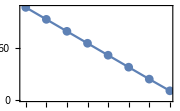

```mathematica
calcNumericDivergence[hilbertComponents]
```

### SU(4) + U(1) chars

#### SU(4) rep {1,0,0} + rep {0,0,1} with opposite U(1) charges

```mathematica
algebraClass=A;
repDynkinLabels={1,0,0};
rank=Length[repDynkinLabels];
dynkinToIrrep[repDynkinLabels,algebraClass]
char1= dynkinToChar[a,repDynkinLabels,algebraClass]
```

4

a_1+a_2+a_3+1/(a_2 a_3 a_1)

```mathematica
algebraClass=A;
repDynkinLabels={0,0,1};
rank=Length[repDynkinLabels];
dynkinToIrrep[repDynkinLabels,algebraClass]
char2= dynkinToChar[a,repDynkinLabels,algebraClass]
```

OverBar[4]

a_1 a_2 a_3+1/a_1+1/a_2+1/a_3

```mathematica
cartanVars=Join[{t},a];
rankTot=Length[repDynkinLabels]+1;
haarU1=1/t;
```

```mathematica
expr=haarU1*haarMeasure[a,algebraClass,rank,type->"Short"] *charToHilbertIntegrand[cartanVars,r,t char1+1/t char2,rankTot]
```

((1-a_1/a_2) (1-a_1/a_3) (1-a_2/a_3) (1-a_1^2 a_2 a_3) (1-a_1 a_2^2 a_3) (1-a_1 a_2 a_3^2))/(a_1 a_2 a_3 t (1-r/(a_1 t)) (1-a_1 r t) (1-r/(a_2 t)) (1-a_2 r t) (1-r/(a_3 t)) (1-(r t)/(a_1 a_2 a_3)) (1-a_3 r t) (1-(a_1 a_2 a_3 r)/t))

```mathematica
{calcTime,hilbertComponents}=calcHilbertIntegral[cartanVars,r,expr,1,rankTot,0,"Branches"]//Timing;
Print["calculation time = ", calcTime, " seconds = ", calcTime/60^2, " hours"];
```

Level = 1

Number of relevant poles = 5

Calculating residue for pole 1/5 in level 1

Calculating residue for pole 2/5 in level 1

Calculating residue for pole 3/5 in level 1

Calculating residue for pole 4/5 in level 1

Calculating residue for pole 5/5 in level 1

Residue for pole 1/5 in level 1 is zero.

Residue for pole 2/5 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 4

Calculating residue for pole 1/4 in level 2

Calculating residue for pole 2/4 in level 2

Calculating residue for pole 3/4 in level 2

Calculating residue for pole 4/4 in level 2

Residue for pole 1/4 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 0

Residue for pole 2/4 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 0

Residue for pole 3/4 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 1

Calculating residue for pole 1/1 in level 3

Residue for pole 1/1 in level 3 is non-zero, sending to level 4

Level = 4

Number of relevant poles = 1

Calculating residue for pole 1/1 in level 4

Residue for pole 4/4 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 1

Calculating residue for pole 1/1 in level 3

Residue for pole 1/1 in level 3 is non-zero, sending to level 4

Level = 4

Number of relevant poles = 1

Calculating residue for pole 1/1 in level 4

Residue for pole 3/5 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 1

Calculating residue for pole 1/1 in level 2

Residue for pole 1/1 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 1

Calculating residue for pole 1/1 in level 3

Residue for pole 1/1 in level 3 is zero.

Residue for pole 4/5 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 1

Calculating residue for pole 1/1 in level 2

Residue for pole 1/1 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 1

Calculating residue for pole 1/1 in level 3

Residue for pole 1/1 in level 3 is non-zero, sending to level 4

Level = 4

Number of relevant poles = 1

Calculating residue for pole 1/1 in level 4

Residue for pole 5/5 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 0

calculation time = 1.53125 seconds = 0.000425347 hours

```mathematica
hilbertComponents//Flatten//Total//Simplify
```

1/(1-r^2)

```mathematica
calcNumericDivergence[hilbertComponents]
```

Numeric divergence degree is -0.998006

-Graphics-

#### SU(4) rep {1,0,1} + singlet with opposite U(1) charges

```mathematica
algebraClass=A;
repDynkinLabels={1,0,1};
rank=Length[repDynkinLabels];
dynkinToIrrep[repDynkinLabels,algebraClass]
char= dynkinToChar[a,repDynkinLabels,algebraClass]
```

15

a_2 a_3 a_1^2+a_2 a_3^2 a_1+a_2^2 a_3 a_1+a_1/a_2+a_1/a_3+a_3/a_2+a_2/a_3+a_2/a_1+a_3/a_1+1/(a_2^2 a_3 a_1)+1/(a_2 a_3^2 a_1)+1/(a_2 a_3 a_1^2)+3

```mathematica
cartanVars=Join[{t},a];
rankTot=Length[repDynkinLabels]+1;
haarU1=1/t;
```

```mathematica
expr=haarU1*haarMeasure[a,algebraClass,rank,type->"Short"] *charToHilbertIntegrand[cartanVars,r,t char+1/t,rankTot]
```

((1-a_1/a_2) (1-a_1/a_3) (1-a_2/a_3) (1-a_1^2 a_2 a_3) (1-a_1 a_2^2 a_3) (1-a_1 a_2 a_3^2))/(a_1 a_2 a_3 t (1-r/t) (1-r t)^3 (1-(a_1 r t)/a_2) (1-(a_2 r t)/a_1) (1-(r t)/(a_1 a_2 a_3^2)) (1-(a_1 r t)/a_3) (1-(r t)/(a_1 a_2^2 a_3)) (1-(r t)/(a_1^2 a_2 a_3)) (1-(a_2 r t)/a_3) (1-(a_3 r t)/a_1) (1-(a_3 r t)/a_2) (1-a_1^2 a_2 a_3 r t) (1-a_1 a_2^2 a_3 r t) (1-a_1 a_2 a_3^2 r t))

```mathematica
{calcTime,hilbertComponents}=calcHilbertIntegral[cartanVars,r,expr,1,rankTot,0,"Branches"]//Timing;
Print["calculation time = ", calcTime, " seconds = ", calcTime/60^2, " hours"];
```

Level = 1

Number of relevant poles = 2

Calculating residue for pole 1/2 in level 1

Calculating residue for pole 2/2 in level 1

Residue for pole 1/2 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 6

Calculating residue for pole 1/6 in level 2

Calculating residue for pole 2/6 in level 2

Calculating residue for pole 3/6 in level 2

Calculating residue for pole 4/6 in level 2

Calculating residue for pole 5/6 in level 2

Calculating residue for pole 6/6 in level 2

Residue for pole 1/6 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 1

Calculating residue for pole 1/1 in level 3

Residue for pole 1/1 in level 3 is non-zero, sending to level 4

Level = 4

Number of relevant poles = 0

Residue for pole 2/6 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 1

Calculating residue for pole 1/1 in level 3

Residue for pole 1/1 in level 3 is non-zero, sending to level 4

Level = 4

Number of relevant poles = 0

Residue for pole 3/6 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 5

Calculating residue for pole 1/5 in level 3

Calculating residue for pole 2/5 in level 3

Calculating residue for pole 3/5 in level 3

Calculating residue for pole 4/5 in level 3

Calculating residue for pole 5/5 in level 3

Residue for pole 1/5 in level 3 is zero.

Residue for pole 2/5 in level 3 is zero.

Residue for pole 3/5 in level 3 is non-zero, sending to level 4

Level = 4

Number of relevant poles = 8

Calculating residue for pole 1/8 in level 4

Residue calculation failed.

Failed residue exists in level 4, return "failed" flag

Residue for pole 4/5 in level 3 is non-zero, sending to level 4

Level = 4

Number of relevant poles = 2

Calculating residue for pole 1/2 in level 4

Calculating residue for pole 2/2 in level 4

Residue for pole 5/5 in level 3 is zero.

Accumulated sick branches {3}/5 in level3

Summing and simplifying the sick branches.

Resending to level4

Level = 4

Number of relevant poles = 8

Calculating residue for pole 1/8 in level 4

Residue calculation failed.

Failed residue exists in level 4, return "failed" flag

Remedying the sick braches failed at level 3

Residue for pole 4/6 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 5

Calculating residue for pole 1/5 in level 3

Calculating residue for pole 2/5 in level 3

Calculating residue for pole 3/5 in level 3

Calculating residue for pole 4/5 in level 3

Calculating residue for pole 5/5 in level 3

Residue for pole 1/5 in level 3 is non-zero, sending to level 4

Level = 4

Number of relevant poles = 4

Calculating residue for pole 1/4 in level 4

Residue calculation failed.

Failed residue exists in level 4, return "failed" flag

Residue for pole 2/5 in level 3 is zero.

Residue for pole 3/5 in level 3 is zero.

Residue for pole 4/5 in level 3 is non-zero, sending to level 4

Level = 4

Number of relevant poles = 2

Calculating residue for pole 1/2 in level 4

Calculating residue for pole 2/2 in level 4

Residue for pole 5/5 in level 3 is zero.

Accumulated sick branches {1}/5 in level3

Summing and simplifying the sick branches.

Resending to level4

Level = 4

Number of relevant poles = 4

Calculating residue for pole 1/4 in level 4

Residue calculation failed.

Failed residue exists in level 4, return "failed" flag

Remedying the sick braches failed at level 3

Residue for pole 5/6 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 6

Calculating residue for pole 1/6 in level 3

Calculating residue for pole 2/6 in level 3

Calculating residue for pole 3/6 in level 3

Calculating residue for pole 4/6 in level 3

Calculating residue for pole 5/6 in level 3

Calculating residue for pole 6/6 in level 3

Residue for pole 1/6 in level 3 is non-zero, sending to level 4

Level = 4

Number of relevant poles = 1

Calculating residue for pole 1/1 in level 4

Residue for pole 2/6 in level 3 is non-zero, sending to level 4

Level = 4

Number of relevant poles = 4

Calculating residue for pole 1/4 in level 4

Residue calculation failed.

Failed residue exists in level 4, return "failed" flag

Residue for pole 3/6 in level 3 is non-zero, sending to level 4

Level = 4

Number of relevant poles = 4

Calculating residue for pole 1/4 in level 4

Residue calculation failed.

Failed residue exists in level 4, return "failed" flag

Residue for pole 4/6 in level 3 is non-zero, sending to level 4

Level = 4

Number of relevant poles = 4

Calculating residue for pole 1/4 in level 4

Residue calculation failed.

Failed residue exists in level 4, return "failed" flag

Residue for pole 5/6 in level 3 is non-zero, sending to level 4

Level = 4

Number of relevant poles = 4

Calculating residue for pole 1/4 in level 4

Calculating residue for pole 2/4 in level 4

Calculating residue for pole 3/4 in level 4

Calculating residue for pole 4/4 in level 4

Residue for pole 6/6 in level 3 is non-zero, sending to level 4

Level = 4

Number of relevant poles = 4

Calculating residue for pole 1/4 in level 4

Calculating residue for pole 2/4 in level 4

Calculating residue for pole 3/4 in level 4

Calculating residue for pole 4/4 in level 4

Accumulated sick branches {2,3,4}/6 in level3

Summing and simplifying the sick branches.

Resending to level4

Level = 4

Number of relevant poles = 4

Calculating residue for pole 1/4 in level 4

Calculating residue for pole 2/4 in level 4

Calculating residue for pole 3/4 in level 4

Calculating residue for pole 4/4 in level 4

Forming a new list of healty branches in level 3

Residue for pole 6/6 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 4

Calculating residue for pole 1/4 in level 3

Calculating residue for pole 2/4 in level 3

Calculating residue for pole 3/4 in level 3

Calculating residue for pole 4/4 in level 3

Residue for pole 1/4 in level 3 is non-zero, sending to level 4

Level = 4

Number of relevant poles = 5

Calculating residue for pole 1/5 in level 4

Calculating residue for pole 2/5 in level 4

Calculating residue for pole 3/5 in level 4

Calculating residue for pole 4/5 in level 4

Calculating residue for pole 5/5 in level 4

Residue for pole 2/4 in level 3 is non-zero, sending to level 4

Level = 4

Number of relevant poles = 5

Calculating residue for pole 1/5 in level 4

Calculating residue for pole 2/5 in level 4

Calculating residue for pole 3/5 in level 4

Calculating residue for pole 4/5 in level 4

Calculating residue for pole 5/5 in level 4

Residue for pole 3/4 in level 3 is non-zero, sending to level 4

Level = 4

Number of relevant poles = 5

Calculating residue for pole 1/5 in level 4

Calculating residue for pole 2/5 in level 4

Calculating residue for pole 3/5 in level 4

Calculating residue for pole 4/5 in level 4

Calculating residue for pole 5/5 in level 4

Residue for pole 4/4 in level 3 is non-zero, sending to level 4

Level = 4

Number of relevant poles = 12

Calculating residue for pole 1/12 in level 4

Calculating residue for pole 2/12 in level 4

Calculating residue for pole 3/12 in level 4

Calculating residue for pole 4/12 in level 4

Calculating residue for pole 5/12 in level 4

Calculating residue for pole 6/12 in level 4

Calculating residue for pole 7/12 in level 4

Calculating residue for pole 8/12 in level 4

Calculating residue for pole 9/12 in level 4

Calculating residue for pole 10/12 in level 4

Calculating residue for pole 11/12 in level 4

Calculating residue for pole 12/12 in level 4

Accumulated sick branches {3,4}/6 in level2

Summing and simplifying the sick branches.

Resending to level3

Level = 3

Number of relevant poles = 5

Calculating residue for pole 1/5 in level 3

Calculating residue for pole 2/5 in level 3

Calculating residue for pole 3/5 in level 3

Calculating residue for pole 4/5 in level 3

Calculating residue for pole 5/5 in level 3

Residue for pole 1/5 in level 3 is non-zero, sending to level 4

Level = 4

Number of relevant poles = 4

Calculating residue for pole 1/4 in level 4

Residue calculation failed.

Failed residue exists in level 4, return "failed" flag

Residue for pole 2/5 in level 3 is zero.

Residue for pole 3/5 in level 3 is non-zero, sending to level 4

Level = 4

Number of relevant poles = 8

Calculating residue for pole 1/8 in level 4

Residue calculation failed.

Failed residue exists in level 4, return "failed" flag

Residue for pole 4/5 in level 3 is non-zero, sending to level 4

Level = 4

Number of relevant poles = 4

Calculating residue for pole 1/4 in level 4

Calculating residue for pole 2/4 in level 4

Calculating residue for pole 3/4 in level 4

Calculating residue for pole 4/4 in level 4

Residue for pole 5/5 in level 3 is zero.

Accumulated sick branches {1,3}/5 in level3

Summing and simplifying the sick branches.

Resending to level4

Level = 4

Number of relevant poles = 0

Forming a new list of healty branches in level 3

Forming a new list of healty branches in level 2

Residue for pole 2/2 in level 1 is zero.

calculation time = 106.719 seconds = 0.0296441 hours

```mathematica
hilbertComponents//Flatten//Total//Simplify
```

-(r^2 (r^6-2 r^4+2))/((r^2-1)^6 (r^2+1)^3 (r^4+1) (r^4+r^2+1))

Numeric divergence degree is -5.96181

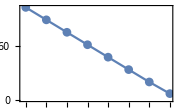

```mathematica
calcNumericDivergence[hilbertComponents]
```